# Simulations of Binary Black Hole Mergers

## Using the Einstein Toolkit

## Importing gravitational waveforms from output of the ET simulation

```mathematica
"C:\\cygwin64\\home"
```

```mathematica
psi4[n_,m_]:=Import["D:\\Computation\\Simulations\\psiGW40\\mp_Psi4_l"<>ToString@n<>"_m"<>ToString@m<>"_r90.00.asc","Table"];
Manipulate[ListLinePlot[Function[x,Transpose[{#[[All,1]],#[[All,x]]}]&@psi4[i,j]]/@{2},PlotRange->All],{{i,2},1,4,1},{{j,2},0,i,1}]
```

## SimulationTools

### Setting up simulation directory

```mathematica
<<SimulationTools`
```

```mathematica
$MultipolePsi4Variable="Psi4";
```

```mathematica
SimulationTools`$SimulationPath={"D:\\Computation\\Simulations"}
```

{D:\Computation\Simulations}

```mathematica
SimulationNames[]
```

{psiBBH,psiGW40}

### Plotting ψ4

```mathematica
psi2290=ReadPsi4["psiBBH",2,2,90]
```

DataTable[<801>,{{0.,200.}}]

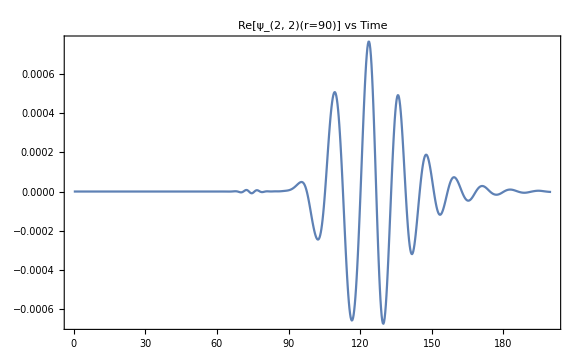

```mathematica
ListPlot[Re@psi2290,PlotRange->All,PlotLabel->"Re[ψ_(2, 2)(r=90)] vs Time",Joined->True,Frame->True]
```

### Calculating and Plotting Strain

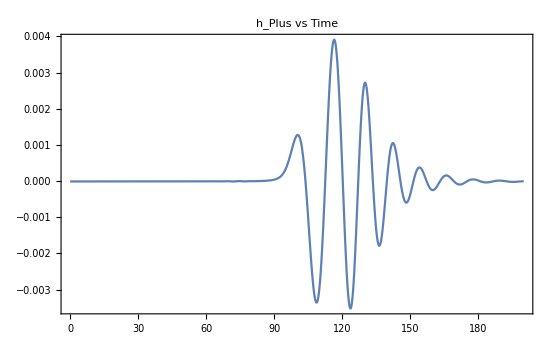

```mathematica
ListPlot[Re@Psi4ToStrain[psi2290,{0,200}],PlotRange->All,PlotLabel->"h_Plus vs Time",Joined->True,Frame->True]
```

### qc0-ratio-timer2

### Plotting orbits

```mathematica
Export["bbhOrbits.csv",ToListOfPoints/@(ReadBinaryCoordinates["qc0-mclachlan-40",#]&/@{1,2})]
```

```mathematica
bbhOrbits=ToExpression@Import["D:\\Computation\\Simulations\\bbhOrbits.csv","Data"];
```

```mathematica
Graphics3D[{Red,Thick,Line[#[[1]]],Blue,Thick,Line[#[[2]]]},PlotRange->All,Axes->True,AxesLabel->{"x","y","z"}]&@bbhOrbits
```

-Graphics3D-

### BBH simulation